```mathematica
f[x_] = Exp[-(q*x)^(c/2)]*x^(-1+c/2)
```

ⅇ^(-(q x)^(c/2)) x^(-1+c/2)

```mathematica
Integrate[f, {x, 0, Infinity}]
```

Integrate::idiv: Integral of f does not converge on {0,∞}.

∫_0^∞ fⅆx

```mathematica
Integrate[f[x],{x, 0, Infinity}]
```

ConditionalExpression[(2 q^(-c/2))/c, Re[c]>0&&Re[q^(c/2)]>0]

```mathematica
Series[Sin[x], {x, 0, 5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
g[x_]=Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g
```

g

```mathematica
g[x]
```

ⅇ^(-(q x)^(c/2)-(p (-1+t+t x))^(c/2)) x^(-1+c/2)

```mathematica
Series[g[x], {x,0,5}]
```

ⅇ^(-(q x)^(c/2)+(-(p (-1+t))^(c/2)-((c (p (-1+t))^(c/2) t) x)/(2 (-1+t))-(((-2+c) c (p (-1+t))^(c/2) t^2) x^2)/(8 (-1+t)^2)-((c (8-6 c+c^2) (p (-1+t))^(c/2) t^3) x^3)/(48 (-1+t)^3)-((c (-48+44 c-12 c^2+c^3) (p (-1+t))^(c/2) t^4) x^4)/(384 (-1+t)^4)-((c (384-400 c+140 c^2-20 c^3+c^4) (p (-1+t))^(c/2) t^5) x^5)/(3840 (-1+t)^5)+O[x]^6)) x^(-1+c/2)

```mathematica
Normal[Series[g[x], {x,0,5}]]
```

ⅇ^(-(p (-1+t))^(c/2)-(c (p (-1+t))^(c/2) t x)/(2 (-1+t))-((-2+c) c (p (-1+t))^(c/2) t^2 x^2)/(8 (-1+t)^2)-(c (8-6 c+c^2) (p (-1+t))^(c/2) t^3 x^3)/(48 (-1+t)^3)-(c (-48+44 c-12 c^2+c^3) (p (-1+t))^(c/2) t^4 x^4)/(384 (-1+t)^4)-(c (384-400 c+140 c^2-20 c^3+c^4) (p (-1+t))^(c/2) t^5 x^5)/(3840 (-1+t)^5)-(q x)^(c/2)) x^(-1+c/2)

```mathematica
Integrate[Normal[Series[g[x], {x,0,5}]], {x,0,Infinity}]
```

∫_0^∞ ⅇ^(-(p (-1+t))^(c/2)-(c (p (-1+t))^(c/2) t x)/(2 (-1+t))-((-2+c) c (p (-1+t))^(c/2) t^2 x^2)/(8 (-1+t)^2)-(c (8-6 c+c^2) (p (-1+t))^(c/2) t^3 x^3)/(48 (-1+t)^3)-(c (-48+44 c-12 c^2+c^3) (p (-1+t))^(c/2) t^4 x^4)/(384 (-1+t)^4)-(c (384-400 c+140 c^2-20 c^3+c^4) (p (-1+t))^(c/2) t^5 x^5)/(3840 (-1+t)^5)-(q x)^(c/2)) x^(-1+c/2)ⅆx

```mathematica
Normal[Series[g[x], {x,0,3}]]
```

ⅇ^(-(p (-1+t))^(c/2)-(c (p (-1+t))^(c/2) t x)/(2 (-1+t))-((-2+c) c (p (-1+t))^(c/2) t^2 x^2)/(8 (-1+t)^2)-(c (8-6 c+c^2) (p (-1+t))^(c/2) t^3 x^3)/(48 (-1+t)^3)-(q x)^(c/2)) x^(-1+c/2)

```mathematica
g[x]
```

ⅇ^(-(q x)^(c/2)-(p (-1+t+t x))^(c/2)) x^(-1+c/2)

```mathematica
ConditionalExpression[p^(-c/2) t^(-c/2) Gamma[c/2,0,(p (-1+t))/q] Gamma[c/2],Re[c]>0&&Re[p/q]>0]
```

ConditionalExpression[p^(-c/2) t^(-c/2) Gamma[c/2] Gamma[c/2,0,(p (-1+t))/q], Re[c]>0&&Re[p/q]>0]

```mathematica
Integrate[E^(-(q x)^(c/2)-(p (-1+t+t x))^(c/2)) x^(-1+c/2),{x,0,Infinity}]
```

∫_0^∞ ⅇ^(-(q x)^(c/2)-(p (-1+t+t x))^(c/2)) x^(-1+c/2)ⅆx

```mathematica
p[x_]=-(q x)^(c/2)-(p (-1+t+t x))^(c/2);
```

```mathematica
p[x]
```

-(q x)^(c/2)-(p (-1+t+t x))^(c/2)

```mathematica
Normal[Series[p[x],{x,0,5}]]
```

-(p (-1+t))^(c/2)-(c (p (-1+t))^(c/2) t x)/(2 (-1+t))-((-2+c) c (p (-1+t))^(c/2) t^2 x^2)/(8 (-1+t)^2)-(c (8-6 c+c^2) (p (-1+t))^(c/2) t^3 x^3)/(48 (-1+t)^3)-(c (-48+44 c-12 c^2+c^3) (p (-1+t))^(c/2) t^4 x^4)/(384 (-1+t)^4)-(c (384-400 c+140 c^2-20 c^3+c^4) (p (-1+t))^(c/2) t^5 x^5)/(3840 (-1+t)^5)-(q x)^(c/2)

```mathematica
Assuming[c=2, Integrate[f[x],{x, 0, Infinity}]]
```

$Assumptions::bass: 2 is not a well-formed assumption.

Integrate::bass: 2 is not a well-formed assumption.

$Assumptions::bass: 2 is not a well-formed assumption.

General::stop: Further output of $Assumptions::bass will be suppressed during this calculation.

Refine::bass: 2 is not a well-formed assumption.

ConditionalExpression[1/q, Re[q]>0]

```mathematica
NIntegrate[g[x], {x, 1, 1000}]
```

NIntegrate::inumr: The integrand ⅇ^(-q x-p (-1+t+t x)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,1000}}.

NIntegrate[g[x],{x,1,1000}]

```mathematica
NIntegrate[g[x],{x,1,Infinity}]
```

NIntegrate::inumr: The integrand ⅇ^(-q x-p (-1+t+t x)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.}}.

NIntegrate[g[x],{x,1,∞}]

```mathematica
Assuming[c=2, Integrate[g[x],{x, 0, Infinity}]]
```

$Assumptions::bass: 2 is not a well-formed assumption.

General::stop: Further output of $Assumptions::bass will be suppressed during this calculation.

Refine::bass: 2 is not a well-formed assumption.

ConditionalExpression[ⅇ^(p-p t)/(q+p t), Re[q+p t]>0]

```mathematica
Assuming[c=1, Integrate[g[x],{x, 0, Infinity}]]
```

$Assumptions::bass: 1 is not a well-formed assumption.

Integrate::bass: 1 is not a well-formed assumption.

$Assumptions::bass: 1 is not a well-formed assumption.

General::stop: Further output of $Assumptions::bass will be suppressed during this calculation.

∫_0^∞ ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)ⅆx

```mathematica
ClearAssumptions[]
```

ClearAssumptions[]

```mathematica
g[x]
```

ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)

```mathematica
g[x_]=Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)

```mathematica
ClearAssumptions[]
```

ClearAssumptions[]

```mathematica
c
```

1

```mathematica
Unset[c]
```

```mathematica
c
```

c

```mathematica
g[x_]=Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-(q x)^(c/2)-(p (-1+t+t x))^(c/2)) x^(-1+c/2)

```mathematica
Assuming[c=1, Integrate[g[x], {x, 0, Infinity}]]
```

$Assumptions::bass: 1 is not a well-formed assumption.

General::stop: Further output of $Assumptions::bass will be suppressed during this calculation.

∫_0^∞ ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)ⅆx

```mathematica
g[x]
```

ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

∫_0^∞ ⅇ^(-√(q x)-√(p (-1+t+t x)))/(√x)ⅆx

```mathematica
c = 3
```

3

```mathematica
c
```

3

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

∫_0^∞ ⅇ^(-(q x)^(3/2)-(p (-1+t+t x))^(3/2)) √xⅆx

```mathematica
Series[g[x], {x, 0, 5}]
```

ⅇ^(-(p (-1+t))^(3/2)) √x-(3 (ⅇ^(-(p (-1+t))^(3/2)) (p (-1+t))^(3/2) t) x^(3/2))/(2 (-1+t))-ⅇ^(-(p (-1+t))^(3/2)) q^(3/2) x^2-1/(8 (-1+t)^2)3 (ⅇ^(-(p (-1+t))^(3/2)) (3 p^3 t^2+(p (-1+t))^(3/2) t^2-9 p^3 t^3+9 p^3 t^4-3 p^3 t^5)) x^(5/2)+(3 ⅇ^(-(p (-1+t))^(3/2)) q^(3/2) (p (-1+t))^(3/2) t x^3)/(2 (-1+t))+1/(16 (-1+t)^3)ⅇ^(-(p (-1+t))^(3/2)) (-8 q^3+24 q^3 t-24 q^3 t^2-6 p^3 t^3+8 q^3 t^3+3 p^3 (-1+t)^3 t^3+(p (-1+t))^(3/2) t^3+9 p^3 (p (-1+t))^(3/2) t^3+18 p^3 t^4-27 p^3 (p (-1+t))^(3/2) t^4-18 p^3 t^5+27 p^3 (p (-1+t))^(3/2) t^5+6 p^3 t^6-9 p^3 (p (-1+t))^(3/2) t^6) x^(7/2)+1/(8 (-1+t)^2)3 ⅇ^(-(p (-1+t))^(3/2)) (3 p^3 q^(3/2) t^2+q^(3/2) (p (-1+t))^(3/2) t^2-9 p^3 q^(3/2) t^3+9 p^3 q^(3/2) t^4-3 p^3 q^(3/2) t^5) x^4+1/(128 (-1+t)^4)3 ⅇ^(-(p (-1+t))^(3/2)) (32 q^3 (p (-1+t))^(3/2) t-96 q^3 (p (-1+t))^(3/2) t^2+96 q^3 (p (-1+t))^(3/2) t^3+3 p^3 t^4+2 p^3 (-1+t)^3 t^4-9 p^6 (-1+t)^3 t^4-(p (-1+t))^(3/2) t^4+18 p^3 (p (-1+t))^(3/2) t^4-32 q^3 (p (-1+t))^(3/2) t^4-9 p^3 t^5+27 p^6 (-1+t)^3 t^5-54 p^3 (p (-1+t))^(3/2) t^5+9 p^3 t^6-27 p^6 (-1+t)^3 t^6+54 p^3 (p (-1+t))^(3/2) t^6-3 p^3 t^7+9 p^6 (-1+t)^3 t^7-18 p^3 (p (-1+t))^(3/2) t^7) x^(9/2)+1/(48 (-1+t)^3)ⅇ^(-(p (-1+t))^(3/2)) (8 q^(9/2)-24 q^(9/2) t+24 q^(9/2) t^2+21 p^3 q^(3/2) t^3-8 q^(9/2) t^3-6 p^3 q^(3/2) (-1+t)^3 t^3-3 q^(3/2) (p (-1+t))^(3/2) t^3-27 p^3 q^(3/2) (p (-1+t))^(3/2) t^3-63 p^3 q^(3/2) t^4+81 p^3 q^(3/2) (p (-1+t))^(3/2) t^4+63 p^3 q^(3/2) t^5-81 p^3 q^(3/2) (p (-1+t))^(3/2) t^5-21 p^3 q^(3/2) t^6+27 p^3 q^(3/2) (p (-1+t))^(3/2) t^6) x^5+O[x]^(11/2)

```mathematica
Plot[g[x], 0, 1000]
```

Plot::nonopt: Options expected (instead of 1000) beyond position 2 in Plot[g[x],0,1000]. An option must be a rule or a list of rules.

Plot[g[x],0,1000]

```mathematica
Plot[g[x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[g[x]]

```mathematica
Plot[g[x],{0,1000}]
```

Plot::pllim: Range specification {0,1000} is not of the form {x, xmin, xmax}.

Plot[g[x],{0,1000}]

```mathematica
Plot[g[x], {x, 0, 1000}]
```

-Graphics-

```mathematica
Plot[g[x], {x, 0, Infinity}]
```

-Graphics-

```mathematica
g[x]
```

ⅇ^(-(q x)^(3/2)-(p (-1+t+t x))^(3/2)) √x

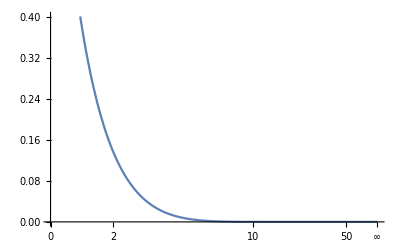

```mathematica
Plot[Exp[-x], {x, 0, Infinity}]
```

```mathematica
g[x_] = Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
Plot[g[x], {x, 0, Infinity}]
```

-Graphics-

```mathematica
Plot[g[x], {x, 0, 1}];
```

```mathematica
g[x_] = Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-(q x)^(3/2)-(p (-1+t+t x))^(3/2)) √x

```mathematica
c = 2
```

2

```mathematica
g[x]
```

ⅇ^(-(q x)^(3/2)-(p (-1+t+t x))^(3/2)) √x

```mathematica
g[x_] = Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-q x-p (-1+t+t x))

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

ConditionalExpression[ⅇ^(p-p t)/(q+p t), Re[q+p t]>0]

```mathematica
Gamma[2]
```

1

```mathematica
Gamma[3]
```

2

```mathematica
g[x]
```

ⅇ^(-q x-p (-1+t+t x))

```mathematica
c = 4
```

4

```mathematica
g[x_] =  Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-q^2 x^2-p^2 (-1+t+t x)^2) x

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

```mathematica
ConditionalExpression[(ⅇ^(-p^2 (-1+t)^2) (√(q^2+p^2 t^2)-ⅇ^((p^4 (-1+t)^2 t^2)/(q^2+p^2 t^2)) p^2 √π (-1+t) t Erfc[(p^2 (-1+t) t)/(√(q^2+p^2 t^2))]))/(2 (q^2+p^2 t^2)^(3/2)), Re[q^2+p^2 t^2]≥0&&(Re[p^2 (-1+t) t]>0||Re[q^2+p^2 t^2]>0)]
```

```mathematica
c
```

c

```mathematica
c=6
```

6

```mathematica
c
```

6

```mathematica
g[x_]=Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-q^3 x^3-p^3 (-1+t+t x)^3) x^2

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

∫_0^∞ ⅇ^(-q^3 x^3-p^3 (-1+t+t x)^3) x^2ⅆx

```mathematica
c=8
```

8

```mathematica
g[x]
```

ⅇ^(-q^3 x^3-p^3 (-1+t+t x)^3) x^2

```mathematica
g[x_]=Exp[-(q*x)^(c/2)-(p*(-1+t+t*x))^(c/2)]*x^(-1+c/2);
```

```mathematica
g[x]
```

ⅇ^(-q^4 x^4-p^4 (-1+t+t x)^4) x^3

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

∫_0^∞ ⅇ^(-q^4 x^4-p^4 (-1+t+t x)^4) x^3ⅆx

```mathematica
Integrate[g[x], x]
```

∫ⅇ^(-q^4 x^4-p^4 (-1+t+t x)^4) x^3ⅆx